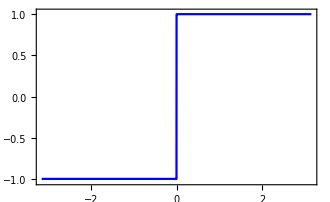

```mathematica
Plot[Sign[x],{x,-π,π},Exclusions->None,PlotRange->{-1.03,1.02},PlotStyle->Blue]
```

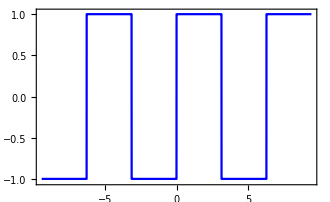

```mathematica
Plot[Sign[Mod[x,2π,-π]],{x,-3π,3π},Exclusions->None,PlotRange->{-1.03,1.02},PlotStyle->Blue]
```

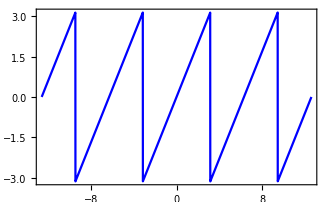

```mathematica
Plot[Mod[x,2π,-π],{x,-4π,4π},PlotStyle->Blue,Exclusions->None]
```

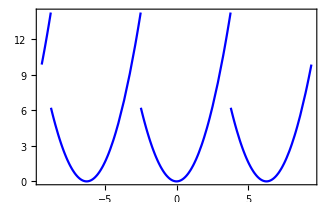

```mathematica
Plot[Mod[x,2π,-2.5]^2,{x,-3π,3π},PlotStyle->Blue]
```

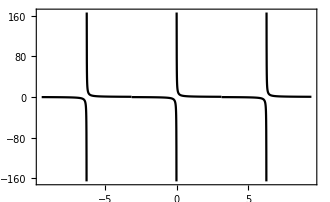

```mathematica
meuplot=Plot[1/Mod[x,2π,-π],{x,-3π,3π}]
```

```mathematica
(* Para salvar um gráfico; ou clique no gráfico e vá em "Save Selection As" *)
Export["filepath.pdf",meuplot]
```

```mathematica
FourierSinCoefficient[Sign[x],x,n]
```

-(2 (-1+(-1)^n))/(n π)

```mathematica
(* n indo de 1 até 20 em passos de 2 *)
Sum[4/(n π)Sin[n x],{n,1,20,2}]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)+(4 Sin[7 x])/(7 π)+(4 Sin[9 x])/(9 π)+(4 Sin[11 x])/(11 π)+(4 Sin[13 x])/(13 π)+(4 Sin[15 x])/(15 π)+(4 Sin[17 x])/(17 π)+(4 Sin[19 x])/(19 π)

```mathematica
Sum[4/(n π)Sin[n x],{n,1,3,2}]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)

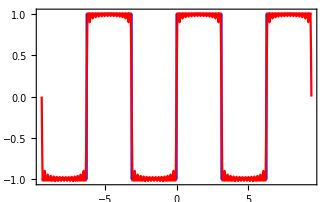

```mathematica
Plot[{
Sign[Mod[x,2π,-π]],
Sum[4/(n π)Sin[n x],{n,1,30,2}]
},{x,-3π,3π},Exclusions->None,PlotRange->{-1.03,1.02},PlotStyle->{Blue,Red}]
```

```mathematica
?Mod
```

# Seção

### Subseção

Texto

∫_0^10 f(x) dx